```mathematica
list = {1,2,3};
list/.List->Sequence
LCM[list/.List->Sequence]
```

Sequence[1,2,3]

6

```mathematica
kIncr = 1/5;
kInit =8;
kCrt = kInit;
kList = {};
```

```mathematica
For[i=0,i<30,i++,
AppendTo[kList,kCrt];
kCrt += kIncr;]
kList
```

{16,159/10,79/5,157/10,78/5,31/2,77/5,153/10,76/5,151/10,15,149/10,74/5,147/10,73/5,29/2,72/5,143/10,71/5,141/10,14,139/10,69/5,137/10,68/5,27/2,67/5,133/10,66/5,131/10}

```mathematica
LCM[kList/.List->Sequence]
```

3243385925479398291162277230563040

```mathematica
crtLCM =1;
listLCM={};
For[i=1,i<=Length[kList],i++,
crtLCM =LCM[crtLCM,kList[[i]]];
AppendTo[listLCM, crtLCM]]
listLCM
```

{16,2544,200976,31553232,410192016,12715952496,979128342192,49935545451792,948775363584048,143265079901191248,716325399505956240,106732484526387479760,3949101927476336751120,27643713492334357257840,2017991084940408079822320,58521741463271834314847280,58521741463271834314847280,58521741463271834314847280,4155043643892300236354156880,195287051262938111108645373360,195287051262938111108645373360,27144900125548397444101706897040,624332702887613141214339258631920,85533580295603000346364478432573040,85533580295603000346364478432573040,256600740886809001039093435297719120,17192249639416203069619260164947181040,17192249639416203069619260164947181040,17192249639416203069619260164947181040,2252184702763522602120123081608080716240}

```mathematica
Length[listLCM]
Length[kList]
```

50

50

```mathematica
ExportString[listLCM,"JavaScriptExpression"]
```

[
	16,
	2544,
	200976,
	31553232,
	410192016,
	12715952496,
	979128342192,
	49935545451792,
	948775363584048,
	143265079901191248,
	716325399505956240,
	106732484526387479760,
	3949101927476336751120,
	27643713492334357257840,
	2017991084940408079822320,
	58521741463271834314847280,
	58521741463271834314847280,
	58521741463271834314847280,
	4155043643892300236354156880,
	195287051262938111108645373360,
	195287051262938111108645373360,
	27144900125548397444101706897040,
	624332702887613141214339258631920,
	85533580295603000346364478432573040,
	85533580295603000346364478432573040,
	256600740886809001039093435297719120,
	17192249639416203069619260164947181040,
	17192249639416203069619260164947181040,
	17192249639416203069619260164947181040,
	2252184702763522602120123081608080716240
]

```mathematica
LCM[8,17/2]
```

```mathematica
136*1.5
```

204.

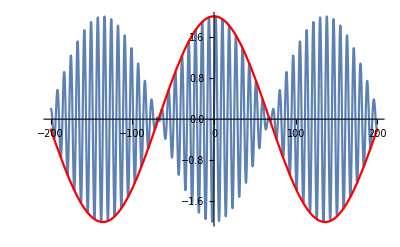

```mathematica
exact=Plot[Sin[2 π/8 x] + Sin[2 π/8.5 x],{x,-200,200}];
envelope =Plot[2Cos[π(1/8 - 1/8.5)x], {x,-200,200}, PlotStyle->Red];
Show[exact,envelope]
```

```mathematica
Solve[(1/8 - 1/8.5)num==1/2,num]
```

{{num→68.}}

```mathematica
k1 = 2Pi;
k2 =  2Pi/2;
```

```mathematica
ω1 = 1/2 k1^2;
ω2 = 1/2 k2^2;
```

```mathematica
Mean[{ω1,ω2}]/Mean[{k1,k2}]//N
```

2.61799

```mathematica
(ω2-ω1)/(k2-k1)//N
```

0.837758

```mathematica
Solve[k num == Pi,num]
```

{{num→4.125}}

```mathematica
x = 4.125;
```

```mathematica
x*8
```

33.

```mathematica
x*40
```

165.

```mathematica
(k*8.25/8 + k*8.25/8.5)/
```

0.762298

```mathematica
Solve[k num == 2 Pi,num]
```

{{num→8.25}}